```mathematica
(* LP QZ 05 - Xiangyu Ren *)
pivot[iStar_,jStar_,tableau_]:=(
kk=Dimensions[tableau][[1]];
nn=Dimensions[tableau][[2]];
newTableau=tableau;
newTableau[[1,jStar]]=tableau[[iStar,nn]];
newTableau[[iStar,nn]]=tableau[[1,jStar]];
For[ii=2,ii≤kk,ii++,
For[jj=1,jj<nn,jj++,
{
If[ii==iStar&&jj==jStar,newTableau[[ii,jj]]=1/tableau[[iStar,jStar]]],
If[ii==iStar&&jj≠jStar,newTableau[[ii,jj]]=-tableau[[ii,jj]]/tableau[[iStar,jStar]]],
If[ii≠iStar&&jj==jStar,newTableau[[ii,jj]]=tableau[[ii,jj]]/tableau[[iStar,jStar]]],
If[ii≠iStar&&jj≠jStar,newTableau[[ii,jj]]=tableau[[ii,jj]]-tableau[[iStar,jj]]tableau[[ii,jStar]]/tableau[[iStar,jStar]]] (* s - qr/p *)
}
]
];
Return[newTableau];
)
```

```mathematica
(* 
Min z = -2x - 4y + 4 
	4x + 3y ≤ 48
	4x + 3y ≥ 24
	-3x + y ≤ 6 
	3x - y ≤ 6 
*)

(* Define the constraint functions and constants *)
Clear[s1,s2,s3,s4,z]
g1[x_,y_]:=4x+3y;
g2[x_,y_]:=4x+3y;
g3[x_,y_]:=-3x+y;
g4[x_,y_]:=3x-y;
b1=48;b2=24;b3=6;b4=6;
s1[x_,y_]:=-g1[x,y]+b1;
s2[x_,y_]:=g2[x,y]-b2;
s3[x_,y_]:=-g3[x,y]+b3;
s4[x_,y_]:=-g4[x,y]+b4;
z[x_,y_]:=-2x-4y+4;

(* Solve for the boundary line functions *)
g1[x_]=y/.Solve[g1[x,y]==b1,{y}][[1,1]];
g2[x_]=y/.Solve[g2[x,y]==b2,{y}][[1,1]];
g3[x_]=y/.Solve[g3[x,y]==b3,{y}][[1,1]];
g4[x_]=y/.Solve[g4[x,y]==b4,{y}][[1,1]];
```

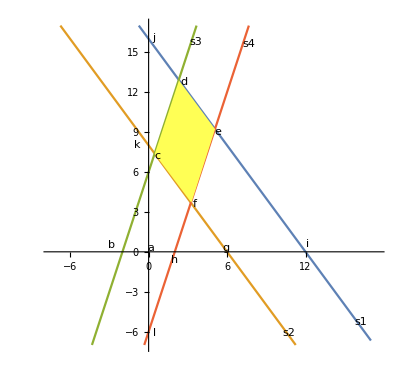

```mathematica
Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-7,17},AspectRatio->Automatic,PlotRange->{-7,17}]
```

```mathematica
m0={"x1","x2","x3","x4",1,""};
m1={-4,4,-3,3,48,"s1"};
m2={4,-4,3,-3,-24,"s2"};
m3={3,-3,-1,1,6,"s3"};
m4={-3,3,1,-1,6,"s4"};
mobj={-2,2,-4,4,4,"z→min"};
a={m0,m1,m2,m3,m4,mobj};
Print["a = ",MatrixForm[a]]
```

a = (x1 | x2 | x3 | x4 | 1 | 
-4 | 4 | -3 | 3 | 48 | s1
4 | -4 | 3 | -3 | -24 | s2
3 | -3 | -1 | 1 | 6 | s3
-3 | 3 | 1 | -1 | 6 | s4
-2 | 2 | -4 | 4 | 4 | z→min)

```mathematica
(* basic solution of a *)
x1=0;x2=0;x3=0;x4=0;ss1=48;ss2=-24;ss3=6;ss4=6;zz=4;
xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 0, y = 0, z = 4

True,True,True,True,True

```mathematica
b=pivot[4,2,a];
Print["b =",MatrixForm[b]]
```

b =(x1 | s3 | x3 | x4 | 1 | 
0 | -4/3 | -13/3 | 13/3 | 56 | s1
0 | 4/3 | 13/3 | -13/3 | -32 | s2
1 | -1/3 | -1/3 | 1/3 | 2 | x2
0 | -1 | 0 | 0 | 12 | s4
0 | -2/3 | -14/3 | 14/3 | 8 | z→min)

```mathematica
(* basic solution of b *)
x1=0;x2=2;x3=0;x4=0;ss1=56;ss2=-32;ss3=0;ss4=12;
zz=8;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = -2, y = 0, z = 8

True,True,True,True,True

```mathematica
c=pivot[3,3,b];
Print["c =",MatrixForm[c]]
```

c =(x1 | s3 | s2 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s1
0 | -4/13 | 3/13 | 1 | 96/13 | x3
1 | -3/13 | -1/13 | 0 | -6/13 | x2
0 | -1 | 0 | 0 | 12 | s4
0 | 10/13 | -14/13 | 0 | -344/13 | z→min)

```mathematica
(* basic solution of c *)
x1=0;x2=-6/13;x3=96/13;x4=0;ss1=24;ss2=0;ss3=0;
ss4=12;zz=-344/13;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 6/13, y = 96/13, z = -344/13

True,True,True,True,True

```mathematica
d=pivot[2,3,c];
Print["d =",MatrixForm[d]]
```

d =(x1 | s3 | s1 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s2
0 | -4/13 | -3/13 | 1 | 168/13 | x3
1 | -3/13 | 1/13 | 0 | -30/13 | x2
0 | -1 | 0 | 0 | 12 | s4
0 | 10/13 | 14/13 | 0 | -680/13 | z→min)

```mathematica
(* basic solution of d *)
x1=0;x2=-30/13;x3=168/13;x4=0;ss1=0;ss2=24;ss3=0;
ss4=12;zz=-680/13;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 30/13, y = 168/13, z = -680/13

True,True,True,True,True

```mathematica
e=pivot[5,2,d];
Print["e =",MatrixForm[e]]
```

e =(x1 | s4 | s1 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s2
0 | 4/13 | -3/13 | 1 | 120/13 | x3
1 | 3/13 | 1/13 | 0 | -66/13 | x2
0 | -1 | 0 | 0 | 12 | s3
0 | -10/13 | 14/13 | 0 | -560/13 | z→min)

```mathematica
(* basic solution of e *)
x1=0;x2=-66/13;x3=120/13;x4=0;ss1=0;ss2=24;ss3=12;
ss4=0;zz=-560/13;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 66/13, y = 120/13, z = -560/13

True,True,True,True,True

```mathematica
f=pivot[2,3,e];
Print["f =",MatrixForm[f]]
```

f =(x1 | s4 | s2 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s1
0 | 4/13 | 3/13 | 1 | 48/13 | x3
1 | 3/13 | -1/13 | 0 | -42/13 | x2
0 | -1 | 0 | 0 | 12 | s3
0 | -10/13 | -14/13 | 0 | -224/13 | z→min)

```mathematica
(* basic solution of f *)
x1=0;x2=-42/13;x3=48/13;x4=0;ss1=24;ss2=0;ss3=12;
ss4=0;zz=-224/13;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 42/13, y = 48/13, z = -224/13

True,True,True,True,True

```mathematica
g=pivot[3,2,f];
Print["g =",MatrixForm[g]]
```

g =(x1 | x3 | s2 | x4 | 1 | 
0 | 0 | -1 | 0 | 24 | s1
0 | 13/4 | -3/4 | -13/4 | -12 | s4
1 | 3/4 | -1/4 | -3/4 | -6 | x2
0 | -13/4 | 3/4 | 13/4 | 24 | s3
0 | -5/2 | -1/2 | 5/2 | -8 | z→min)

```mathematica
(* basic solution of g *)
x1=0;x2=-6;x3=0;x4=0;ss1=24;ss2=0;ss3=24;
ss4=-12;zz=-8;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 6, y = 0, z = -8

True,True,True,True,True

```mathematica
h=pivot[3,3,g];
Print["h =",MatrixForm[h]]
```

h =(x1 | x3 | s4 | x4 | 1 | 
0 | -13/3 | 4/3 | 13/3 | 40 | s1
0 | 13/3 | -4/3 | -13/3 | -16 | s2
1 | -1/3 | 1/3 | 1/3 | -2 | x2
0 | 0 | -1 | 0 | 12 | s3
0 | -14/3 | 2/3 | 14/3 | 0 | z→min)

```mathematica
(* basic solution of h *)
x1=0;x2=-2;x3=0;x4=0;ss1=40;ss2=-16;ss3=12;
ss4=0;zz=0;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 2, y = 0, z = 0

True,True,True,True,True

```mathematica
i=pivot[2,3,h];
Print["i =",MatrixForm[i]]
```

i =(x1 | x3 | s1 | x4 | 1 | 
0 | 13/4 | 3/4 | -13/4 | -30 | s4
0 | 0 | -1 | 0 | 24 | s2
1 | 3/4 | 1/4 | -3/4 | -12 | x2
0 | -13/4 | -3/4 | 13/4 | 42 | s3
0 | -5/2 | 1/2 | 5/2 | -20 | z→min)

```mathematica
(* basic solution of i *)
x1=0;x2=-12;x3=0;x4=0;ss1=0;ss2=24;ss3=42;
ss4=-30;zz=-20;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 12, y = 0, z = -20

True,True,True,True,True

```mathematica
j=pivot[4,2,i];
Print["j =",MatrixForm[j]]
```

j =(x1 | x2 | s1 | x4 | 1 | 
-13/3 | 13/3 | -1/3 | 0 | 22 | s4
0 | 0 | -1 | 0 | 24 | s2
-4/3 | 4/3 | -1/3 | 1 | 16 | x3
13/3 | -13/3 | 1/3 | 0 | -10 | s3
10/3 | -10/3 | 4/3 | 0 | -60 | z→min)

```mathematica
(* basic solution of j *)
x1=0;x2=0;x3=16;x4=0;ss1=0;ss2=24;ss3=-10;
ss4=22;zz=-60;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 0, y = 16, z = -60

True,True,True,True,True

```mathematica
k=pivot[3,3,j];
Print["k =",MatrixForm[k]]
```

k =(x1 | x2 | s2 | x4 | 1 | 
-13/3 | 13/3 | 1/3 | 0 | 14 | s4
0 | 0 | -1 | 0 | 24 | s1
-4/3 | 4/3 | 1/3 | 1 | 8 | x3
13/3 | -13/3 | -1/3 | 0 | -2 | s3
10/3 | -10/3 | -4/3 | 0 | -28 | z→min)

```mathematica
(* basic solution of k *)
x1=0;x2=0;x3=8;x4=0;ss1=24;ss2=0;ss3=-2;
ss4=14;zz=-28;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 0, y = 8, z = -28

True,True,True,True,True

```mathematica
l=pivot[2,3,k];
Print["l =",MatrixForm[l]]
```

l =(x1 | x2 | s4 | x4 | 1 | 
13 | -13 | 3 | 0 | -42 | s2
-13 | 13 | -3 | 0 | 66 | s1
3 | -3 | 1 | 1 | -6 | x3
0 | 0 | -1 | 0 | 12 | s3
-14 | 14 | -4 | 0 | 28 | z→min)

```mathematica
(* basic solution of l *)
x1=0;x2=0;x3=-6;x4=0;ss1=66;ss2=-42;ss3=12;
ss4=0;zz=28;xx=x1-x2;yy=x3-x4;
Print["x = ",xx,", y = ",yy,", z = ",zz]
Print[s1[xx,yy]==ss1,",",s2[xx,yy]==ss2,",",s3[xx,yy]==ss3,",",s4[xx,yy]==ss4,",",z[xx,yy]==zz]
```

x = 0, y = -6, z = 28

True,True,True,True,True